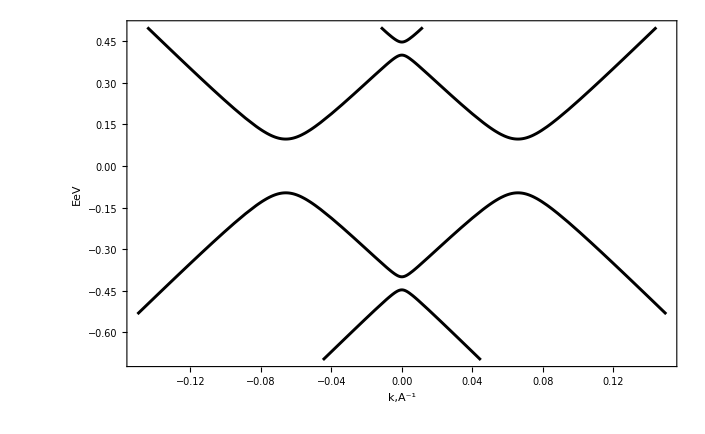

```mathematica
Clear["Global`*"]
tp:=0.4; d1:=0.1; d2:=-0.1;  c:=6.25;  
A[U_]:=0;
B[x_,U_]:=-2*((d1^2+d2^2)/(2)+U^2+(c*x)^2+tp^2);
C1[x_,U_]:=2*U*(d1^2-d2^2);
D1[x_,U_]:=(d1^2-d2^2)*U+d1^2*(c*x)^2-2*d1*d2*tp^2+U^4-U^2*d2^2-2*U^2*(c*x)^2+2*U^2*tp^2+d2^2*(c*x)^2+(c*x)^4-2*(c*x)^2*tp^2+tp^4;
H2[x_,U__]:=A[U]*C1[x,U]-4*D1[x,U];
H3[x_,U_]:=4*B[x,U]*D1[x,U]-C1[x,U]^2-A[U]^2*D1[x,U];
p[x_,U_]:=-B[x,U]^2/3+H2[x,U];
q[x_,U_]:=-2*B[x,U]^3/27+B[x,U]*H2[x,U]/3+H3[x,U];
Y[x_,U_]:=(-q[x,U]/2+((q[x,U]^2)/4+(p[x,U]^3)/27)^(1/2))^(1/3)+(-q[x,U]/2-((q[x,U]^2)/4+(p[x,U]^3)/27)^(1/2))^(1/3);
s1[x_,U_]=Y[x,U]+(B[x,U])/(3);
b11[x_,U_]:=(A[U])/(2)+Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]];
b22[x_,U_]:=(A[U])/(2)-Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]];
c11[x_,U_]:=(s1[x,U])/2+((A[U]*s1[x,U])/(2)-C1[x,U])/(2*Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]]);
c22[x_,U_]:=(s1[x,U])/2-(A[U]*s1[x,U]/2-C1[x,U])/(2*Sqrt[(A[U]^2)/(4)-B[x,U]+s1[x,U]]);
f1[x_,U_]:=(-b11[x,U]+√(b11[x,U]^2-4*c11[x,U]))/2;  
f2[x_,U__]:=(-b11[x,U]-(b11[x,U]^2-4*c11[x,U])^(1/2))/2;
f3[x_,U_]:=(-b22[x,U]+(b22[x,U]^2-4*c22[x,U])^(1/2))/2;
 f4[x_,U_]:=(-b22[x,U]-(b22[x,U]^2-4*c22[x,U])^(1/2))/2;  


Plot[{{f1[x,U],f2[x,U],f3[x,U],f4[x,U]}/.U->{0.1}},{x,-0.15,0.15},AxesLabel->{"k,A^-1",EeV},PlotRange->{-0.7,0.5},PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Red}},Frame->True]
```

```mathematica
d1:=0.05
data1=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]],x][[1]]},{α,-0.35,0.35,0.01}];
d1:=-0.05
data2=Table[{α,NMinimize[Re[f4[x,α]-f1[x,α]],x][[1]]},{α,-0.35,0.35,0.01}];
```

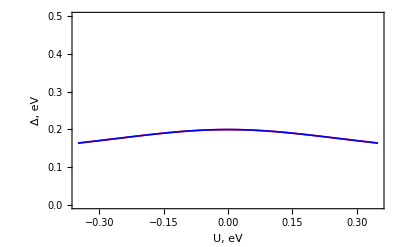

```mathematica
ListPlot[{data1,data2},Joined->True,PlotStyle-> {{Thickness[0.003],Red},{Thickness[0.003],Blue}},PlotRange->{0,0.5},FrameLabel->{"U, eV","Δ, eV"},Frame->True]
```